### Init

```mathematica
n=8;
g=GridGraph[{n,n}];
```

```mathematica
temperatureTable=Table[RandomReal[],n^2];

initialCircleCondition={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,2,2,2,2,0,0,0,0,2,2,2,2,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};

hg1={{1,2},{1,9},{2,1},{2,3},{2,10},{3,2},{3,4},{3,11},{4,3},{4,5},{4,12},{5,4},{5,6},{5,13},{6,5},{6,7},{6,14},{7,6},{7,8},{7,15},{8,7},{8,16},{9,1},{9,10},{9,17},{10,2},{10,9},{10,11},{10,18},{11,3},{11,10},{11,12},{11,19},{12,4},{12,11},{12,13},{12,20},{13,5},{13,12},{13,14},{13,21},{14,6},{14,13},{14,15},{14,22},{15,7},{15,14},{15,16},{15,23},{16,8},{16,15},{16,24},{17,9},{17,18},{17,25},{18,10},{18,17},{18,19},{18,26},{19,11},{19,18},{19,20},{19,27},{20,12},{20,19},{20,21},{20,28},{21,13},{21,20},{21,22},{21,29},{22,14},{22,21},{22,23},{22,30},{23,15},{23,22},{23,24},{23,31},{24,16},{24,23},{24,32},{25,17},{25,26},{25,33},{26,18},{26,25},{26,27},{26,34},{27,19},{27,26},{27,28},{27,35},{28,20},{28,27},{28,29},{28,36},{29,21},{29,28},{29,30},{29,37},{30,22},{30,29},{30,31},{30,38},{31,23},{31,30},{31,32},{31,39},{32,24},{32,31},{32,40},{33,25},{33,34},{33,41},{34,26},{34,33},{34,35},{34,42},{35,27},{35,34},{35,36},{35,43},{36,28},{36,35},{36,37},{36,44},{37,29},{37,36},{37,38},{37,45},{38,30},{38,37},{38,39},{38,46},{39,31},{39,38},{39,40},{39,47},{40,32},{40,39},{40,48},{41,33},{41,42},{41,49},{42,34},{42,41},{42,43},{42,50},{43,35},{43,42},{43,44},{43,51},{44,36},{44,43},{44,45},{44,52},{45,37},{45,44},{45,46},{45,53},{46,38},{46,45},{46,47},{46,54},{47,39},{47,46},{47,48},{47,55},{48,40},{48,47},{48,56},{49,41},{49,50},{49,57},{50,42},{50,49},{50,51},{50,58},{51,43},{51,50},{51,52},{51,59},{52,44},{52,51},{52,53},{52,60},{53,45},{53,52},{53,54},{53,61},{54,46},{54,53},{54,55},{54,62},{55,47},{55,54},{55,56},{55,63},{56,48},{56,55},{56,64},{57,49},{57,58},{58,50},{58,57},{58,59},{59,51},{59,58},{59,60},{60,52},{60,59},{60,61},{61,53},{61,60},{61,62},{62,54},{62,61},{62,63},{63,55},{63,62},{63,64},{64,56},{64,63}};
```

```mathematica
k=0.1;δt=0.5;
```

```mathematica
ruleSet=ResourceFunction["EnumerateWolframModelRules"][{{2,2}}->{{2,2}}];
```

ResourceObject::updav: There is an update available for resource "ParallelMapMonitored". Use ResourceUpdate[ParallelMapMonitored] to get the update.

```mathematica
RulePlot[ResourceFunction["WolframModel"]@ruleSet[[489]],VertexLabels->Automatic,"RulePartsAspectRatio"->0.5]
```

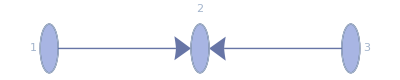

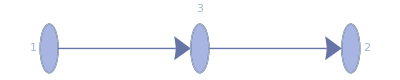

```mathematica
ResourceFunction["WolframModelPlot"][{{1,2},{3,2}},VertexLabels->Automatic]
ResourceFunction["WolframModelPlot"][{{1,3},{3,2}},VertexLabels->Automatic]
```

```mathematica
ruleSet[[489]]
```

{{1,2},{3,2}}→{{1,3},{3,2}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{{x,y}}->{{x,y},{y,z}}}],VertexLabels->Automatic,"RulePartsAspectRatio"->0.25]
```

```mathematica
graphToHypergraphNew[g_]:=Flatten[DeleteCases[Table[If[(Normal@AdjacencyMatrix@g)[[#]][[i]]*i==0,0,{#,i}],{i,VertexList@g}],0]&/@(VertexList@g),1]

rwLaplacian[g_]:=IdentityMatrix[Length@VertexList@g]-Dot[Inverse@Normal@DiagonalMatrix[VertexOutDegree@g],Normal@AdjacencyMatrix[g]]

dynamicDiscreteLaplacian[G_,ϕ_]:=Dot[IdentityMatrix[Length@VertexList@G]-Dot[Inverse@Normal@DiagonalMatrix[VertexOutDegree@G],Normal@AdjacencyMatrix[G]],ϕ]

dynamicDiscreteLaplacian2[G_,ϕ_]:=Dot[IdentityMatrix[Length@VertexList@G]-Dot[PseudoInverse@Normal@DiagonalMatrix[VertexOutDegree@G],Normal@AdjacencyMatrix[G]],ϕ]

EulerMethod489[{HG_,t_,ϕ_}]:={ResourceFunction["WolframModel"][#,HG,1,"FinalState"]&[ruleSet[[489]]],t+δt,ϕ-k*δt *dynamicDiscreteLaplacian[ResourceFunction["HypergraphToGraph"]@HG,ϕ]} 

EulerMethod4892[{HG_,t_,ϕ_}]:={ResourceFunction["WolframModel"][#,HG,1,"FinalState"]&[ruleSet[[489]]],t+δt,ϕ-k*δt *dynamicDiscreteLaplacian2[ResourceFunction["HypergraphToGraph"]@HG,ϕ]} 

listEvolution[r_,InitialCondition_]:=NestWhileList[
ResourceFunction["WolframModel"][r,#1,1,"FinalState"]&,
InitialCondition,
(!IsomorphicGraphQ[SimpleGraph@Graph[UndirectedEdge@@@#1],SimpleGraph@Graph[UndirectedEdge@@@#2]]&&ResourceFunction["ConnectedHypergraphQ"][#1])& ,
2,100
]

EulerMethodStatic[{HG_,t_,ϕ_}]:={HG,t+δt,ϕ-k*δt *dynamicDiscreteLaplacian[ResourceFunction["HypergraphToGraph"]@HG,ϕ]}
```

```mathematica
gif5=Module[{data=NestList[EulerMethod489,{hg1,0,initialCircleCondition},40]},Table[Graph[UndirectedEdge@@@ResourceFunction["HypergraphToGraph"]@data[[1,1]],
GraphLayout->{"GridEmbedding","Dimension"->{8,8}},
VertexStyle->Thread[Range[VertexCount@ResourceFunction["HypergraphToGraph"]@data[[i,1]]]->ColorData["TemperatureMap"]/@data[[i,3]]],
VertexSize->1,VertexLabels->None,EdgeStyle->Thickness[0]],{i,40}]];
```

```mathematica
`
```

## Statistical investigation

We now have a working model of heat transfer on graphs obeying the Wolfram Model rules. The rule 489 is especially interesting, as it leaves the Hausdorff dimension of the graph approximately = 3.

```mathematica
listEvolution[ruleSet[[489]],hg1]
```

{1}
 |  |  |  |

```mathematica
hausdorffDimension489=Module[{rule=ruleSet[[489]]},ResourceFunction["WolframHausdorffDimension"][SimpleGraph[Graph[UndirectedEdge@@@#]],All,{1,1},"VertexMethod"->Mean]&/@listEvolution[rule,hg1]]
```

{2.15514,2.66227,2.89346,2.82673,2.80501,2.78675,2.81704,2.81985,2.82783,2.85418,2.8583,2.84932,2.83344,2.85041,2.86149,2.8829,2.88306,2.89089,2.90695,2.87238,2.87183,2.89252,2.89349,2.8871,2.87888,2.85095,2.89853,2.9198,2.88361,2.93529,2.92743,2.92794,2.90756,2.89573,2.89146,2.92501,2.87818,2.87472,2.89592,2.90511,2.89549,2.8866,2.8624,2.9144,2.9152,2.89083,2.89234,2.91185,2.91719,2.89867,2.90562,2.86673,2.88737,2.86575,2.85316,2.86014,2.87556,2.87825,2.88727,2.89198,2.90731,2.89727,2.90214,2.85357,2.85645,2.88648,2.88745,2.89705,2.88599,2.92391,2.92488,2.90534,2.90213,2.922,2.92311,2.90708,2.89712,2.90053,2.90833,2.93185,2.9207,2.91639,2.91145,2.89167,2.87509,2.88076,2.89556,2.87897,2.89042,2.87587,2.85567,2.89049,2.89205,2.90593,2.89519,2.92046,2.92958,2.90576,2.89096,2.9029,2.86885}

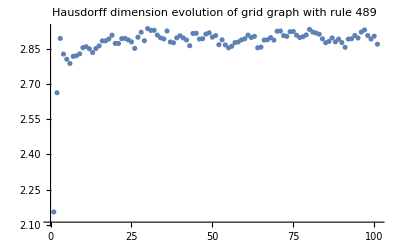

```mathematica
ListPlot[hausdorffDimension489,PlotRange->All,PlotLabel->"Hausdorff dimension evolution of grid graph with rule 489"]
```

```mathematica
p0=Variance/@NestList[EulerMethodStatic,{hg1,0,temperatureTable},100][[All,3]];
```

```mathematica
p489=Variance/@NestList[EulerMethod489,{hg1,0,temperatureTable},100][[All,3]];
```

The fixed graph variance decay is asymptotically hyperbolic, while the rule 489 decay is exponential:

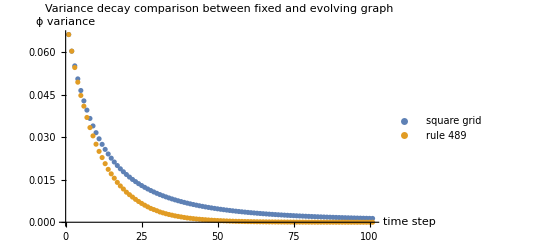

```mathematica
ListPlot[{p0,p489},PlotLabel->"Variance decay comparison between fixed and evolving graph",PlotLegends->{"square grid","rule 489"},PlotRange->All,AxesLabel->{"time step","ϕ variance"}]
```

All of the eigenvalues are non-negative, with one zero value. This value gives the asymptotic behaviour of the system (the average initial temperature at time infinity ).

```mathematica
hg2={{2,1},{1,3},{3,2}};
initialCondition2 = {2,0,0};
```

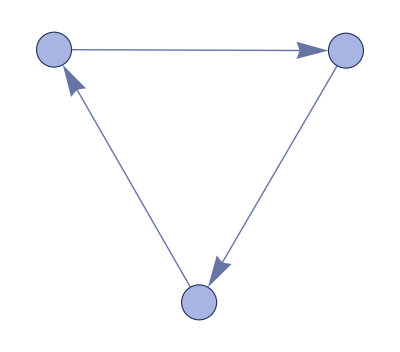

```mathematica
ResourceFunction["WolframModelPlot"]@hg2
```

```mathematica
gif2=Module[{data=NestList[EulerMethod4892,{hg2,0,initialCondition2},40]},Table[Graph[UndirectedEdge@@@ResourceFunction["HypergraphToGraph"]@data[[i,1]],
VertexStyle->Thread[Range[VertexCount@ResourceFunction["HypergraphToGraph"]@data[[i,1]]]->ColorData["TemperatureMap"]/@data[[i,3]]],
VertexSize->0.1,VertexLabels->None,EdgeStyle->Thickness[0.005]],{i,40}]];
```

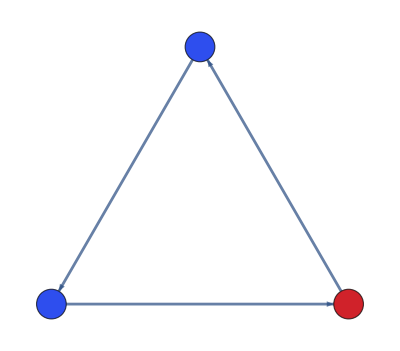

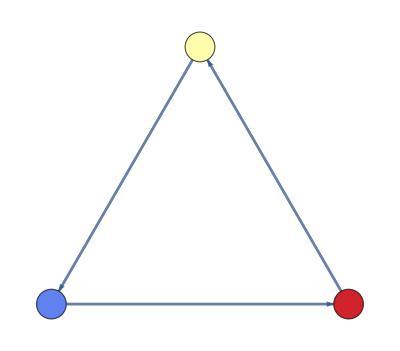

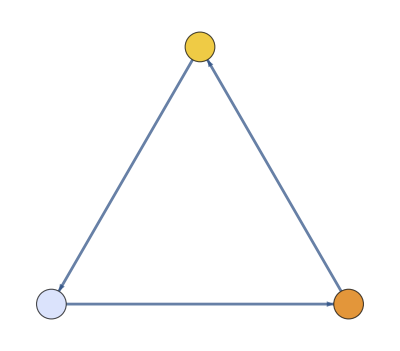

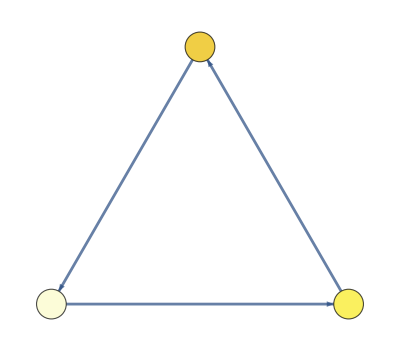

```mathematica
gif2[[1]]
gif2[[10]]
gif2[[20]]
gif2[[30]]
```

```mathematica
rwLaplacian[ResourceFunction["HypergraphToGraph"]@hg2]
```

{{1,-1,0},{0,1,-1},{-1,0,1}}

```mathematica
MatrixForm[{{1,-1,0},{0,1,-1},{-1,0,1}}]
```

(1 | -1 | 0
0 | 1 | -1
-1 | 0 | 1)

```mathematica
TeXForm[({{1, -1, 0}, {0, 1, -1}, {-1, 0, 1}})]
```

\left(
\begin{array}{ccc}
 1 & -1 & 0 \\
 0 & 1 & -1 \\
 -1 & 0 & 1 \\
\end{array}
\right)

```mathematica
Eigenvalues@rwLaplacian[ResourceFunction["HypergraphToGraph"]@hg2]
```

```mathematica
TeXForm@{1/2 (3+ⅈ √3),1/2 (3-ⅈ √3),0}
```

\left\{\frac{1}{2} \left(3+i \sqrt{3}\right),\frac{1}{2} \left(3-i \sqrt{3}\right),0\right\}

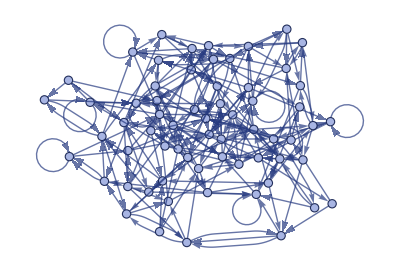

```mathematica
ResourceFunction["WolframModelPlot"]@ResourceFunction["WolframModel"][#,hg1,8,"FinalState"]&[ruleSet[[489]]]
```

```mathematica
hg3= ResourceFunction["WolframModel"][#,hg1,8,"FinalState"]&[ruleSet[[489]]];
gif3=Module[{data=NestList[EulerMethodStatic,{hg3,0,initialCircleCondition},100]},Table[Graph[UndirectedEdge@@@ResourceFunction["HypergraphToGraph"]@data[[i,1]],
VertexStyle->Thread[Range[VertexCount@ResourceFunction["HypergraphToGraph"]@data[[i,1]]]->ColorData["TemperatureMap"]/@data[[i,3]]],
VertexSize->1,VertexLabels->None,EdgeStyle->Automatic],{i,100}]];
```

```mathematica
gif3[[1]]
gif3[[20]]
gif3[[40]]
gif3[[60]]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

## Eigenvalue investigation

```mathematica
Re@N@Eigenvalues@rwLaplacian@ResourceFunction["HypergraphToGraph"][ResourceFunction["WolframModel"][ruleSet[[489]],hg1,100,"FinalState"]]
```

{1.518,1.45866,1.45866,1.41306,1.41306,1.37605,1.37605,1.40531,1.34593,1.34593,1.368,1.368,1.22436,1.22436,1.26139,1.26139,1.27276,1.23768,1.20016,1.20016,1.12403,1.12403,1.14959,1.14959,1.1022,1.1022,1.05337,1.05337,0.976876,0.976876,0.924589,0.924589,1.00962,1.00962,1.01202,1.01202,0.973808,0.936079,0.936079,0.857672,0.857672,0.918765,0.795133,0.795133,0.843517,0.837009,0.837009,0.745763,0.745763,0.788597,0.788597,0.712223,0.712223,0.612673,0.612673,0.651758,0.621262,0.621262,0.565532,0.565532,0.583195,0.583195,0.48499,0.}

Time series of the Laplacian eigenvalues

```mathematica
hGSeries = NestList[EulerMethod489,{hg1,0,temperatureTable},100]
```

{{1},99,{{{8,53},{46,56},{22,31},{42,62},{38,45},{19,7},{52,5},{16,21},{15,63},{15,42},{56,17},{25,36},{59,30},{30,22},{39,23},{24,54},{64,35},{53,60},{60,50},{14,58},{55,16},{22,19},{1,27},{40,6},{4,44},{57,46},{46,47},{43,29},{18,2},{20,15},164,{52,10},{10,32},{3,32},{32,18},{38,50},{50,27},{16,21},{21,51},{37,51},{51,19},{42,19},{19,46},{6,45},{45,47},{47,7},{7,1},{12,6},{6,4},{60,44},{44,12},{11,29},{29,2},{5,2},{2,38},{58,15},{15,55},{25,59},{59,20},{10,20},{20,20}},50.,{1}}}
 |  |  |  |

```mathematica
eigenSeries = Re@N@Eigenvalues@rwLaplacian@ResourceFunction["HypergraphToGraph"][#] & /@ hGSeries[[All, 1]]
```

{{2.,1.95369,1.95369,1.90097,1.82491,1.82491,1.7635,1.7635,1.64017,1.64017,1.62349,1.56757,1.56757,1.4342,1.4342,1.42365,1.42365,1.35145,1.35145,1.24211,1.24211,1.22252,1.20236,1.20236,1.15269,1.15269,1.09213,1.09213,1.,1.,1.,1.,1.,1.,1.,1.,0.907868,0.907868,0.84731,0.84731,0.797643,0.797643,0.777479,0.757889,0.757889,0.648545,0.648545,0.576348,0.576348,0.5658,0.5658,0.432428,0.432428,0.37651,0.359834,0.359834,0.236501,0.236501,0.175093,0.175093,0.0990311,0.0463094,0.0463094,0.},{1.44867,1.44867,1.4185,1.4185,1.4092,1.4092,1.37347,1.37347,1.37712,1.37712,1.37216,1.37216,1.40013,1.28378,1.28378,1.25658,1.25658,1.29813,1.29813,1.34743,1.34743,1.33677,1.30316,1.30316,1.24686,1.24686,1.21423,1.21423,1.11473,1.11473,1.23273,1.23273,1.17269,1.17269,1.13925,1.13925,1.07186,1.07186,1.03001,1.03001,1.03108,0.94665,0.94665,0.869253,0.869253,0.881745,0.790314,0.790314,0.696672,0.696672,0.603685,0.603685,0.528784,0.528784,0.466158,0.369883,0.369883,0.296504,0.23299,0.23299,0.138286,0.0954635,0.05626,0.},{1.38418,1.38418,1.4407,1.4407,1.44916,1.44916,1.32141,1.32141,1.29761,1.29761,1.31576,1.31576,1.2618,1.22637,1.22637,1.18289,1.18289,1.21586,1.1952,1.1952,1.20603,1.20603,1.11358,1.11358,0.886593,0.886593,1.04448,1.04448,1.0866,1.0866,1.11481,1.11481,0.966659,0.966659,1.05277,1.05277,0.837763,0.837763,0.960637,0.960637,0.909615,0.909615,0.986582,0.986582,0.977162,0.977162,0.954206,0.954206,0.915703,0.915703,0.824135,0.824135,0.768196,0.68717,0.68717,0.630062,0.485634,0.485634,0.396477,0.322518,0.199486,0.143128,0.0823205,0.},{1.56259,1.56259,1.5053,1.42309,1.42309,1.42263,1.42263,1.39541,1.25229,1.25229,1.30514,1.30514,1.33213,1.33213,1.32112,1.32112,1.23753,1.23753,1.28507,1.28507,1.22348,1.22348,1.23201,1.13991,1.13991,1.04015,1.04015,1.11538,1.11538,1.12082,1.12082,1.04199,1.04199,0.966089,0.966089,0.913495,0.913495,0.830928,0.830928,0.947028,0.947028,0.707018,0.707018,0.883605,0.883605,0.632916,0.632916,0.761861,0.761861,0.82154,0.82154,0.77324,0.77324,0.734477,0.734477,0.764645,0.744739,0.58971,0.58971,0.442881,0.240443,0.240443,0.0803627,0.},{1.57593,1.4752,1.45575,1.45575,1.44082,1.44082,1.39619,1.39619,1.39762,1.39762,1.29544,1.29544,1.30453,1.30453,1.29812,1.29812,1.23914,1.23914,1.24862,1.24862,1.18231,1.11176,1.11176,1.05739,1.05739,1.11006,0.989846,0.989846,1.03966,1.03966,0.9614,0.9614,1.02126,1.02126,0.860645,0.860645,0.8807,0.8807,0.889513,0.889513,0.855483,0.855483,0.851532,0.851532,0.784014,0.784014,0.724033,0.724033,0.805821,0.591787,0.591787,0.750403,0.750403,0.645219,0.645219,0.581309,0.581309,0.633487,0.633487,0.547783,0.331493,0.331493,0.11185,0.},{1.49113,1.49113,1.4861,1.4861,1.45754,1.40459,1.40459,1.34463,1.34463,1.38208,1.38208,1.26749,1.26749,1.282,1.276,1.276,1.21711,1.21711,1.14478,1.14478,1.17878,1.17878,1.1944,1.15382,1.15382,1.07257,1.07257,1.06525,1.06525,1.06603,1.01243,1.01243,0.959479,0.959479,0.911652,0.911652,0.939606,0.939606,0.803827,0.803827,0.883636,0.883636,0.815544,0.815544,0.85819,0.841388,0.733734,0.733734,0.750281,0.750281,0.706092,0.706092,0.669716,0.669716,0.636436,0.503422,0.503422,0.54164,0.54164,0.546179,0.546179,0.350924,0.123304,0.},{1.4831,1.4831,1.48728,1.44249,1.44249,1.35323,1.35323,1.36448,1.36448,1.2554,1.2554,1.31144,1.22853,1.22853,1.23828,1.23828,1.14231,1.14231,1.17856,1.17856,1.15438,1.15438,1.16413,1.1271,1.1271,1.0684,1.0684,1.0771,1.02088,1.02088,0.929385,0.929385,0.988026,0.946041,0.946041,0.916539,0.916539,0.848855,0.848855,0.921126,0.921126,0.787252,0.787252,0.794485,0.794485,0.810587,0.793891,0.793891,0.718106,0.718106,0.654408,0.654408,0.714002,0.701573,0.674674,0.674674,0.563302,0.51524,0.51524,0.460235,0.460235,0.405553,0.158911,0.},{1.5532,1.52324,1.52324,1.46056,1.46056,1.44108,1.44108,1.38248,1.38248,1.39157,1.33277,1.33277,1.29544,1.29544,1.30892,1.30892,1.18215,1.18215,1.1825,1.1825,1.21176,1.05217,1.05217,1.17392,1.09376,1.09376,1.0984,1.02318,1.02318,0.918644,0.918644,0.96577,0.96577,1.00644,0.900468,0.900468,0.93991,0.93991,0.853962,0.842146,0.842146,0.800816,0.800816,0.731237,0.731237,0.787006,0.734989,0.734989,0.662818,0.662818,0.716048,0.716048,0.616947,0.616947,0.635057,0.635057,0.622697,0.622697,0.514121,0.514121,0.470367,0.402592,0.29095,0.},{1.51999,1.48731,1.48731,1.40468,1.40468,1.419,1.419,1.39489,1.39489,1.31241,1.31241,1.29885,1.29885,1.21964,1.21964,1.15322,1.15322,1.22168,1.22168,1.15409,1.15409,1.0938,1.0938,1.11188,1.11188,1.0299,1.0299,1.07624,1.07624,1.03275,0.990962,0.990962,0.973743,0.973743,0.871584,0.871584,0.931329,0.931329,0.920013,0.920013,0.824468,0.824468,0.848418,0.729663,0.729663,0.743998,0.743998,0.721712,0.721712,0.624936,0.624936,0.634365,0.634365,0.662449,0.662449,0.64656,0.567423,0.567423,0.519988,0.519988,0.515619,0.515619,0.399333,0.},{1.45639,1.45639,1.45346,1.4126,1.37474,1.37474,1.32785,1.32785,1.24224,1.24224,1.29973,1.29973,1.25807,1.25807,1.29744,1.29744,1.27056,1.27056,1.20023,1.20023,1.1496,1.1496,1.13763,1.13763,1.08123,1.08123,1.14686,1.05313,1.05313,0.94806,0.94806,1.01109,1.01109,0.905665,0.905665,0.970389,0.970389,0.991276,0.909729,0.909729,0.913036,0.836922,0.836922,0.856202,0.726284,0.726284,0.748702,0.748702,0.743028,0.743028,0.683493,0.683493,0.644944,0.644944,0.648808,0.648808,0.573918,0.573918,0.575452,0.495949,0.495949,0.480018,0.34612,0.},{1.5069,1.48431,1.48431,1.46255,1.46255,1.33316,1.33316,1.28531,1.28531,1.34388,1.34388,1.3362,1.3362,1.1964,1.1964,1.24663,1.24663,1.20567,1.20567,1.2048,1.2048,1.1082,1.1082,1.18421,1.16221,1.16221,1.05354,1.05354,1.038,1.038,0.926147,0.926147,0.946668,0.946668,0.991764,0.991764,1.00149,1.00149,0.84904,0.84904,0.850325,0.850325,0.774526,0.774526,0.817344,0.817344,0.727859,0.727859,0.773777,0.773777,0.748922,0.748922,0.706457,0.706457,0.597436,0.597436,0.612304,0.564144,0.564144,0.518042,0.513878,0.387235,0.387235,0.},{1.48492,1.42267,1.42267,1.41066,1.41066,1.40857,1.40857,1.38625,1.38625,1.31882,1.31882,1.30412,1.30412,1.26815,1.26815,1.21407,1.21407,1.18856,1.18856,1.11373,1.11373,1.18741,1.18741,1.0589,1.0589,1.09891,1.09891,1.10791,1.10791,1.05194,0.931694,0.931694,1.01222,0.96022,0.96022,0.870235,0.870235,0.940662,0.940662,0.817676,0.817676,0.851253,0.851253,0.829978,0.829978,0.840898,0.83578,0.78774,0.78774,0.713055,0.713055,0.693163,0.693163,0.707193,0.617045,0.617045,0.58497,0.58497,0.596751,0.596751,0.527066,0.420156,0.420156,0.},{1.54443,1.49144,1.44928,1.44087,1.44087,1.42275,1.42275,1.32488,1.32488,1.30798,1.30798,1.30111,1.30111,1.24156,1.24156,1.21473,1.21473,1.26524,1.26524,1.2459,1.2459,1.11558,1.11558,1.07283,1.07283,1.08716,1.08716,0.974351,0.974351,1.00446,1.00446,1.03247,1.03247,1.01386,1.01386,0.973466,0.973466,0.896875,0.896875,0.857023,0.857023,0.744604,0.744604,0.755613,0.755613,0.786652,0.786652,0.698379,0.698379,0.772404,0.733514,0.733514,0.663408,0.663408,0.679111,0.679111,0.67368,0.571184,0.571184,0.487148,0.487148,0.492546,0.417458,0.},{1.50072,1.49775,1.49775,1.47011,1.43091,1.43091,1.38855,1.38855,1.35165,1.35165,1.27076,1.27076,1.26873,1.26873,1.23597,1.23597,1.14478,1.14478,1.1977,1.1977,1.17042,1.17042,1.17734,1.17734,1.16863,1.16863,1.1598,1.06635,1.06635,0.961405,0.961405,1.02958,1.02958,0.908643,0.908643,0.977392,0.977392,0.939684,0.939684,0.903914,0.903914,0.934783,0.900386,0.900386,0.761666,0.761666,0.796888,0.796888,0.732455,0.732455,0.735284,0.642564,0.642564,0.66409,0.66409,0.599852,0.599852,0.574124,0.574124,0.545349,0.545349,0.417121,0.417121,0.},{1.50788,1.50788,1.45552,1.45552,1.43874,1.36536,1.36536,1.3573,1.3573,1.32589,1.32589,1.24493,1.24493,1.27632,1.27632,1.22454,1.15339,1.15339,1.12193,1.12193,1.18725,1.18725,1.15162,1.15162,1.04774,1.04774,1.05667,1.05667,1.09616,1.06284,1.06284,0.976489,0.976489,0.988962,0.988962,1.00324,0.958808,0.958808,0.855525,0.855525,0.742914,0.742914,0.864582,0.864582,0.865642,0.721592,0.721592,0.767456,0.767456,0.738157,0.738157,0.628996,0.628996,0.670593,0.670593,0.563938,0.563938,0.592594,0.592594,0.558294,0.465425,0.465425,0.445359,0.},{1.49617,1.46302,1.46302,1.40724,1.40724,1.38937,1.3242,1.3242,1.35556,1.35556,1.26878,1.26878,1.17879,1.17879,1.2252,1.2252,1.26069,1.26069,1.22478,1.22478,1.14942,1.14942,1.15083,1.08085,1.08085,1.09923,1.09923,1.07377,1.07377,1.05163,0.94312,0.94312,0.924053,0.924053,0.951985,0.951985,0.847183,0.847183,0.904442,0.904442,0.933696,0.933696,0.798234,0.798234,0.833948,0.833948,0.837109,0.797659,0.797659,0.796814,0.634281,0.634281,0.707975,0.644463,0.644463,0.604959,0.604959,0.576274,0.576274,0.559918,0.559918,0.526871,0.41175,0.},{1.50057,1.50057,1.47696,1.47696,1.39482,1.39482,1.30062,1.30062,1.34363,1.34363,1.34119,1.34119,1.30687,1.30687,1.25838,1.25838,1.27392,1.27392,1.20401,1.20401,1.16932,1.16932,1.10826,1.10826,1.13681,1.03408,1.03408,0.989647,0.989647,1.04298,1.04298,0.946548,0.946548,1.013,1.013,1.,0.983984,0.974532,0.974532,0.949747,0.949747,0.899291,0.899291,0.833713,0.833713,0.763664,0.763664,0.733789,0.733789,0.70243,0.70243,0.755715,0.702196,0.702196,0.602564,0.602564,0.558483,0.558483,0.582725,0.559324,0.559324,0.548534,0.439823,0.},{1.44389,1.44389,1.44173,1.44173,1.44185,1.40286,1.40286,1.35121,1.35121,1.37793,1.31547,1.28075,1.28075,1.28889,1.28889,1.24205,1.24205,1.18392,1.18392,1.15069,1.15069,1.18888,1.18888,1.08023,1.08023,1.12714,1.12714,1.10019,1.05685,1.05685,1.04948,1.00365,1.00365,0.945983,0.945983,0.930488,0.930488,0.929453,0.929453,0.83067,0.83067,0.90441,0.90441,0.784668,0.784668,0.843722,0.843722,0.747581,0.747581,0.725559,0.725559,0.756904,0.756904,0.670565,0.670565,0.649309,0.649309,0.608683,0.608683,0.53454,0.53454,0.533888,0.470622,0.},{1.48087,1.48087,1.47331,1.47331,1.35134,1.35134,1.38458,1.31144,1.31144,1.33703,1.33703,1.3257,1.3257,1.2128,1.2128,1.15979,1.15979,1.27109,1.27109,1.20558,1.20558,1.19331,1.19331,1.11864,1.11864,1.13368,1.13368,1.0298,1.0298,1.08246,1.00315,1.00315,1.02686,1.02686,0.954738,0.954738,1.02537,0.923913,0.923913,0.933139,0.933139,0.964302,0.87602,0.87602,0.860242,0.781559,0.781559,0.745749,0.745749,0.659442,0.659442,0.763005,0.763005,0.748063,0.674358,0.674358,0.61265,0.61265,0.604461,0.604461,0.554975,0.554975,0.498187,0.},{1.48092,1.48092,1.47556,1.47556,1.41894,1.41894,1.38694,1.34567,1.34567,1.29421,1.29421,1.28555,1.28555,1.27556,1.27556,1.20124,1.20124,1.14006,1.14006,1.0965,1.0965,1.17883,1.05901,1.05901,1.11827,1.11827,1.112,1.112,1.07022,1.07022,1.08353,1.08353,0.974846,0.974846,0.916272,0.916272,1.01845,0.985518,0.985518,0.874163,0.874163,0.945037,0.945037,0.869509,0.809711,0.809711,0.795125,0.795125,0.737851,0.737851,0.671748,0.671748,0.68901,0.68901,0.590844,0.590844,0.638258,0.638258,0.57822,0.57822,0.560044,0.560044,0.51515,0.},{1.53156,1.45801,1.45801,1.41316,1.41316,1.35022,1.35022,1.34648,1.336,1.336,1.31562,1.31562,1.29881,1.29881,1.23683,1.23683,1.14425,1.14425,1.20961,1.20961,1.21758,1.21758,1.21628,1.21628,1.05869,1.05869,1.06811,1.06811,1.03545,1.03545,1.02785,1.02785,1.02654,1.02654,0.88254,0.88254,0.935561,0.935561,0.960271,0.906922,0.906922,0.854399,0.854399,0.750723,0.750723,0.780583,0.780583,0.767018,0.767018,0.661279,0.661279,0.731551,0.731551,0.65309,0.65309,0.644955,0.644955,0.56029,0.56029,0.586803,0.586803,0.49382,0.49382,0.},{1.5074,1.5074,1.38348,1.38348,1.42307,1.42307,1.33444,1.33444,1.35023,1.32037,1.32037,1.20873,1.20873,1.26661,1.26661,1.26378,1.26378,1.15155,1.15155,1.15427,1.15427,1.04545,1.04545,1.12173,1.12173,1.04771,1.04771,1.05168,1.05168,1.08385,1.08385,1.06347,1.05671,1.,0.892939,0.892939,0.969201,0.969201,0.907426,0.907426,0.907687,0.907687,0.791841,0.791841,0.882967,0.768403,0.768403,0.808691,0.808691,0.78003,0.752466,0.752466,0.703624,0.703624,0.645462,0.645462,0.642489,0.642489,0.609197,0.609197,0.536286,0.536286,0.433544,0.},{1.49454,1.49454,1.49291,1.49291,1.41992,1.41992,1.36777,1.31666,1.31666,1.27575,1.27575,1.23199,1.23199,1.28463,1.25974,1.25974,1.19612,1.19612,1.11542,1.11542,1.15948,1.15948,1.13571,1.13571,1.0984,1.0984,1.11811,1.11811,1.11819,1.01841,1.01841,0.967036,0.967036,0.867459,0.867459,0.895934,0.895934,0.966489,0.966489,0.869181,0.869181,0.878042,0.878042,0.912302,0.903922,0.903922,0.797838,0.797838,0.730428,0.730428,0.791503,0.70362,0.70362,0.69404,0.69404,0.625425,0.625425,0.583373,0.583373,0.495079,0.495079,0.535107,0.535107,0.},{1.49029,1.49029,1.46637,1.46637,1.45165,1.42559,1.42559,1.35106,1.35106,1.32238,1.20324,1.20324,1.25491,1.25491,1.24871,1.24871,1.20098,1.20098,1.10972,1.10972,1.09589,1.09589,1.12645,1.12645,1.14815,1.14815,1.0063,1.0063,1.09714,1.09714,1.02113,1.02113,0.959123,0.959123,0.862272,0.862272,0.922746,0.922746,0.795362,0.795362,0.919001,0.90094,0.90094,0.827176,0.827176,0.769433,0.769433,0.840284,0.840284,0.824351,0.824351,0.753148,0.753148,0.630468,0.630468,0.657505,0.622662,0.622662,0.565589,0.525697,0.525697,0.556069,0.485302,0.},{1.50946,1.50946,1.44613,1.44613,1.3614,1.3614,1.34231,1.34231,1.35681,1.35681,1.328,1.328,1.28193,1.28193,1.19473,1.19473,1.24701,1.24701,1.20349,1.20349,1.21151,1.21151,1.14586,1.14586,1.13331,1.09102,1.09102,1.05859,1.05859,0.98503,0.98503,1.02699,1.02699,0.976227,0.976227,0.927816,0.927816,0.97911,0.949824,0.949824,0.850484,0.850484,0.783085,0.783085,0.837198,0.837198,0.678848,0.678848,0.763654,0.763654,0.782303,0.782303,0.674128,0.674128,0.672181,0.672181,0.675867,0.675867,0.67805,0.533233,0.476463,0.476463,0.499572,0.},{1.52623,1.52623,1.48525,1.37238,1.37238,1.37899,1.37899,1.38263,1.32141,1.32141,1.35915,1.35915,1.24309,1.24309,1.1859,1.1859,1.21689,1.21689,1.23378,1.23378,1.24325,1.21874,1.21874,1.13183,1.13183,1.14205,1.14205,1.00181,1.00181,1.0544,1.0544,1.04558,1.04041,1.04041,0.976463,0.976463,0.857959,0.857959,0.94825,0.909037,0.909037,0.881969,0.881969,0.805562,0.805562,0.813163,0.813163,0.648472,0.648472,0.663317,0.663317,0.697604,0.697604,0.706304,0.682503,0.652236,0.652236,0.651614,0.651614,0.499799,0.499799,0.518861,0.518861,0.},{1.50731,1.48098,1.48098,1.40183,1.40183,1.34057,1.34057,1.34698,1.34698,1.35205,1.35205,1.30096,1.30096,1.19015,1.19015,1.24873,1.24873,1.19402,1.19402,1.18572,1.18572,1.19048,1.19048,1.05078,1.05078,1.16625,1.09116,1.09116,1.10536,1.10536,1.02483,1.02483,1.03812,1.03812,0.98285,0.98285,0.919077,0.919077,0.811413,0.811413,0.817402,0.817402,0.87798,0.87798,0.896702,0.831532,0.831532,0.731132,0.731132,0.738323,0.738323,0.718317,0.718317,0.668961,0.668961,0.627691,0.627691,0.584327,0.584327,0.592859,0.54982,0.54982,0.533807,0.},{1.508,1.43638,1.43638,1.3971,1.3971,1.34216,1.34216,1.37975,1.37975,1.28981,1.28981,1.30664,1.30664,1.29347,1.27863,1.21221,1.21221,1.16739,1.16739,1.23176,1.23176,1.18378,1.18378,1.10491,1.10491,1.051,1.051,1.13472,1.08046,1.08046,0.878565,0.878565,0.935701,0.935701,1.00741,1.00741,0.908834,0.908834,0.956466,0.956466,0.879992,0.879992,0.89042,0.876814,0.876814,0.7936,0.7936,0.819681,0.819681,0.740318,0.740318,0.669534,0.669534,0.734317,0.696994,0.696994,0.632207,0.632207,0.578096,0.578096,0.538746,0.538746,0.467825,0.},{1.48152,1.48152,1.48747,1.43015,1.43015,1.40842,1.40842,1.36786,1.36786,1.2759,1.2759,1.28023,1.28023,1.30721,1.30721,1.25004,1.12651,1.12651,1.16174,1.16174,1.16729,1.16729,1.10414,1.10414,1.14002,1.00899,1.00899,1.0581,1.0581,1.0129,1.0129,1.04757,1.04757,0.945743,0.945743,0.951586,0.951586,0.887194,0.887194,0.955971,0.955971,0.849849,0.849849,0.768211,0.768211,0.841211,0.81984,0.81984,0.764453,0.764453,0.748119,0.748119,0.647876,0.647876,0.691218,0.691218,0.613993,0.613993,0.536069,0.536069,0.576419,0.576419,0.541104,0.},{1.488,1.44556,1.44556,1.41016,1.41016,1.38153,1.34898,1.34898,1.32141,1.32141,1.24335,1.24335,1.24878,1.24878,1.25244,1.25244,1.15337,1.15337,1.22522,1.22522,1.20204,1.20204,1.15048,1.15048,1.00154,1.00154,1.11755,1.1121,1.09082,1.09082,0.996889,0.996889,0.924001,0.924001,0.890824,0.890824,0.957703,0.957703,0.928031,0.928031,0.945248,0.828254,0.828254,0.782953,0.782953,0.866005,0.845155,0.845155,0.832802,0.832802,0.759271,0.759271,0.654403,0.654403,0.713389,0.611331,0.611331,0.640773,0.591745,0.591745,0.556406,0.516981,0.516981,0.},{1.55117,1.49974,1.49974,1.43155,1.39913,1.36517,1.36517,1.32245,1.32245,1.23126,1.23126,1.25058,1.25058,1.27681,1.27681,1.23149,1.13576,1.13576,1.2021,1.2021,1.17326,1.17326,1.10185,1.10185,1.15799,1.15799,1.04383,1.04383,1.06645,1.06645,1.03185,1.03185,1.00261,1.00261,0.872084,0.872084,0.882021,0.882021,0.919053,0.919053,0.916107,0.916107,0.843,0.843,0.762688,0.762688,0.83852,0.83852,0.754752,0.754752,0.734598,0.734598,0.748825,0.748825,0.739199,0.57864,0.57864,0.575864,0.575864,0.613833,0.613833,0.578522,0.515556,0.},{1.53424,1.43804,1.43804,1.41244,1.41244,1.34408,1.34408,1.29177,1.29177,1.33234,1.33234,1.31186,1.31186,1.24604,1.24604,1.19498,1.19498,1.19956,1.19956,1.13124,1.13124,1.16039,1.16039,1.1494,1.12991,1.12991,1.10624,1.10624,1.03011,1.03011,0.941657,0.941657,1.01534,0.878632,0.878632,0.977965,0.949326,0.949326,0.893323,0.893323,0.924355,0.924355,0.770423,0.770423,0.83549,0.83549,0.821062,0.821062,0.774686,0.774686,0.755936,0.755936,0.738457,0.622279,0.622279,0.666658,0.614233,0.614233,0.645687,0.645687,0.562409,0.562409,0.530938,0.},{1.52947,1.46419,1.46419,1.43981,1.43981,1.37506,1.37506,1.35479,1.35479,1.30786,1.30786,1.31173,1.31173,1.22659,1.22659,1.25193,1.25193,1.27418,1.21507,1.21507,1.2068,1.2068,1.1148,1.1148,1.12248,1.06374,1.06374,0.987581,0.987581,0.950498,0.950498,1.06364,1.06364,0.916126,0.916126,0.98423,0.98423,0.944825,0.944825,0.953303,0.905894,0.905894,0.809743,0.809743,0.738718,0.738718,0.811617,0.811617,0.822245,0.787604,0.787604,0.706299,0.706299,0.70556,0.70556,0.621099,0.621099,0.590566,0.590566,0.577297,0.577297,0.590498,0.590498,0.},{1.52837,1.52837,1.45472,1.45472,1.38877,1.38877,1.41313,1.32153,1.32153,1.33805,1.33805,1.33762,1.23443,1.23443,1.278,1.278,1.24325,1.24325,1.15914,1.15914,1.15249,1.15249,1.03347,1.03347,1.11429,1.11429,0.989025,0.989025,1.0365,1.0365,1.04909,1.03522,1.03522,0.939938,0.939938,0.885734,0.885734,0.93851,0.858078,0.858078,0.876017,0.876017,0.881736,0.881736,0.785668,0.785668,0.791898,0.791898,0.685371,0.685371,0.751993,0.751993,0.669091,0.669091,0.688911,0.688911,0.561928,0.561928,0.66315,0.57239,0.57239,0.586257,0.500223,0.},{1.47392,1.4572,1.4572,1.42298,1.37944,1.37944,1.38,1.38,1.37205,1.37205,1.37228,1.26429,1.26429,1.29802,1.2488,1.2488,1.16757,1.16757,1.21366,1.21366,1.21887,1.21887,1.03515,1.03515,1.06066,1.06066,1.09224,1.08692,1.08692,1.0529,1.0529,0.876827,0.876827,0.926124,0.926124,0.956511,0.956511,0.972918,0.972918,0.951212,0.826952,0.826952,0.863079,0.863079,0.863616,0.863616,0.82853,0.754458,0.754458,0.760081,0.675453,0.675453,0.701236,0.701236,0.68629,0.68629,0.636548,0.636548,0.583853,0.503864,0.503864,0.55207,0.55207,0.},{1.49185,1.49185,1.49705,1.42931,1.42931,1.37976,1.37976,1.33088,1.33088,1.36573,1.36573,1.32563,1.32563,1.18342,1.18342,1.23446,1.23446,1.1965,1.1965,1.20191,1.20191,1.111,1.111,1.17482,1.10489,1.10489,1.00961,1.00961,1.06908,0.945668,0.945668,1.02388,1.02388,0.992245,0.992245,0.915605,0.915605,0.830128,0.830128,0.883008,0.883008,0.911387,0.911387,0.881751,0.881751,0.828257,0.828257,0.752426,0.752426,0.65161,0.65161,0.732793,0.732793,0.712259,0.65615,0.65615,0.621917,0.621917,0.664459,0.664459,0.569221,0.569221,0.595908,0.},{1.46592,1.44102,1.44102,1.419,1.419,1.38887,1.38887,1.33817,1.33817,1.36571,1.36571,1.35821,1.30443,1.30443,1.31192,1.31192,1.27269,1.23509,1.23509,1.1376,1.1376,1.12678,1.12678,1.11695,0.984261,0.984261,1.01831,1.01831,1.08702,0.983314,0.983314,1.02282,1.02282,0.978293,0.978293,0.875332,0.875332,0.94365,0.94365,0.913505,0.913505,0.849729,0.849729,0.869916,0.869916,0.823319,0.823319,0.815691,0.815691,0.710379,0.710379,0.733946,0.733946,0.647993,0.647993,0.645957,0.597517,0.597517,0.533772,0.533772,0.531507,0.531507,0.49958,0.},{1.45914,1.45914,1.4478,1.42644,1.42644,1.39781,1.38872,1.38872,1.29219,1.29219,1.31299,1.31299,1.27799,1.27799,1.18919,1.18919,1.22708,1.22708,1.21916,1.21916,1.16242,1.16242,1.09141,1.09141,1.11383,1.11383,1.09878,1.08107,1.08107,1.01094,1.01094,0.989591,0.989591,1.06099,1.06099,0.908549,0.908549,0.921541,0.921541,0.887159,0.887159,0.900324,0.806709,0.806709,0.733939,0.733939,0.822498,0.822498,0.707691,0.707691,0.757194,0.678567,0.678567,0.682686,0.682686,0.602032,0.547432,0.547432,0.568356,0.568356,0.570059,0.544741,0.544741,0.},{1.56176,1.56176,1.43036,1.43036,1.44595,1.44595,1.44779,1.32598,1.32598,1.35833,1.33152,1.33152,1.2869,1.2869,1.22206,1.22206,1.25995,1.25995,1.11727,1.11727,1.18654,1.18654,1.05637,1.05637,1.05136,1.05136,1.08232,1.08232,1.08592,1.08592,1.08017,0.998655,0.998655,0.947483,0.947483,0.957368,0.957368,0.959667,0.913411,0.913411,0.82283,0.82283,0.827408,0.827408,0.799516,0.799516,0.726795,0.726795,0.684391,0.684391,0.78103,0.735282,0.627231,0.627231,0.678835,0.678835,0.631901,0.631901,0.666606,0.569899,0.569899,0.547803,0.41336,0.},{1.51149,1.42985,1.42985,1.43922,1.43922,1.42598,1.39455,1.2823,1.2823,1.26583,1.26583,1.25588,1.25588,1.27784,1.27784,1.25593,1.25593,1.16821,1.16821,1.22065,1.22065,1.07378,1.07378,1.12195,1.12195,1.04754,1.04754,1.03097,1.03097,1.10156,1.10156,1.03502,1.03502,1.03529,0.949501,0.949501,0.936627,0.936627,0.82489,0.82489,0.747537,0.747537,0.857173,0.857173,0.847181,0.847181,0.76903,0.76903,0.76412,0.654307,0.654307,0.683428,0.683428,0.715644,0.715644,0.684598,0.684598,0.661134,0.622593,0.55844,0.55844,0.527448,0.504319,0.},{1.52001,1.52001,1.45041,1.45041,1.37547,1.37547,1.31473,1.31473,1.35487,1.26382,1.26382,1.30289,1.30289,1.30731,1.23196,1.23196,1.2362,1.2362,1.1458,1.1458,1.13197,1.13197,1.02963,1.02963,1.12111,1.12111,1.12478,1.12478,1.08061,1.0171,1.0171,0.943518,0.943518,1.01096,1.01096,0.99838,0.99838,0.922959,0.922959,0.921984,0.921984,0.832465,0.832465,0.784865,0.784865,0.84301,0.736561,0.736561,0.767697,0.767697,0.738639,0.738639,0.757715,0.655233,0.655233,0.653688,0.653688,0.585557,0.585557,0.582142,0.55327,0.525472,0.525472,0.},{1.45474,1.45474,1.45883,1.45883,1.42108,1.39565,1.39565,1.35296,1.35296,1.35937,1.35937,1.27836,1.27836,1.32849,1.27821,1.27821,1.21309,1.21309,1.24211,1.24211,1.20138,1.03532,1.03532,1.07822,1.07822,1.12557,1.12557,1.00749,1.00749,1.02148,1.02148,1.02464,1.02464,0.911638,0.911638,1.00689,1.00689,1.008,0.944161,0.892291,0.892291,0.832866,0.832866,0.761937,0.761937,0.851624,0.851624,0.661662,0.661662,0.78356,0.78356,0.71184,0.71184,0.649542,0.649542,0.669426,0.669426,0.576981,0.576981,0.533169,0.516668,0.516668,0.507802,0.},{1.59034,1.48289,1.48289,1.48288,1.48288,1.39426,1.39426,1.37764,1.37764,1.33683,1.33683,1.30073,1.30073,1.35066,1.25658,1.25658,1.19461,1.19461,1.23758,1.23758,1.14145,1.14145,1.13242,1.13242,1.02369,1.02369,1.05719,1.05719,1.08001,1.08001,1.04062,0.97625,0.97625,0.926395,0.926395,0.881852,0.881852,0.940682,0.940682,0.813796,0.813796,0.895127,0.895127,0.832168,0.832168,0.746688,0.746688,0.784415,0.768247,0.768247,0.63001,0.63001,0.724131,0.645549,0.645549,0.620971,0.620971,0.626237,0.626237,0.598758,0.598758,0.478425,0.478425,0.},{1.44609,1.43606,1.43606,1.39232,1.39232,1.42263,1.33504,1.33504,1.33803,1.33267,1.33267,1.29829,1.29829,1.22158,1.22158,1.22605,1.22605,1.21563,1.15449,1.15449,1.0715,1.0715,1.10013,1.10013,1.13997,1.13997,1.15127,1.15127,1.15171,1.03054,1.03054,1.00192,1.00192,0.881361,0.881361,0.952085,0.952085,0.886448,0.886448,0.924338,0.924338,0.90615,0.875641,0.875641,0.767697,0.767697,0.782205,0.782205,0.788763,0.788763,0.753568,0.666846,0.666846,0.677468,0.677468,0.694693,0.556588,0.556588,0.567642,0.567642,0.554909,0.554909,0.440534,0.},{1.55573,1.55573,1.4169,1.40337,1.40337,1.37109,1.37109,1.34962,1.34962,1.32517,1.32517,1.34096,1.34096,1.19898,1.19898,1.20468,1.20468,1.2009,1.14688,1.14688,1.10767,1.10767,1.06985,1.06985,1.04429,1.04429,1.09461,1.09461,1.09934,1.09934,0.911173,0.911173,0.946038,0.946038,1.02407,0.971014,0.971014,0.974864,0.892863,0.892863,0.824724,0.824724,0.770753,0.770753,0.847872,0.802865,0.802865,0.805982,0.805982,0.705079,0.705079,0.791519,0.688641,0.688641,0.699579,0.699579,0.576807,0.576807,0.613626,0.613626,0.545363,0.545363,0.527026,0.},{1.50652,1.45575,1.45575,1.4359,1.4359,1.40515,1.40515,1.29438,1.29438,1.35378,1.35378,1.33489,1.29273,1.29273,1.26453,1.26453,1.21317,1.21317,1.09361,1.09361,1.16651,1.16651,1.13052,1.13052,1.1255,1.08988,1.08988,1.03123,1.03123,0.998645,0.998645,1.02254,1.02254,0.896401,0.896401,0.911132,0.911132,0.978158,0.978158,0.897527,0.897527,0.797047,0.797047,0.815959,0.815959,0.731379,0.731379,0.796369,0.796369,0.677797,0.677797,0.716351,0.716351,0.735223,0.735223,0.630345,0.630345,0.585614,0.585614,0.548477,0.548477,0.528078,0.489454,0.},{1.53074,1.53074,1.49783,1.45231,1.45231,1.43423,1.43423,1.35177,1.35177,1.27008,1.27008,1.2893,1.2893,1.23022,1.23022,1.1867,1.1867,1.19825,1.19825,1.13325,1.13325,1.17137,1.11733,1.11733,1.03302,1.03302,1.04963,1.04963,1.11755,1.11755,1.06093,1.06093,1.04294,1.026,0.996969,0.996969,0.950294,0.950294,0.930131,0.930131,0.814761,0.814761,0.879755,0.844019,0.844019,0.756429,0.756429,0.758384,0.758384,0.663776,0.663776,0.753777,0.747941,0.747941,0.686054,0.686054,0.694026,0.597901,0.597901,0.521242,0.521242,0.493919,0.493919,0.},{1.50766,1.50766,1.42138,1.42138,1.41445,1.41445,1.39855,1.39855,1.33867,1.33867,1.25929,1.25929,1.28424,1.28424,1.21384,1.21384,1.17706,1.17706,1.20308,1.20308,1.12595,1.12595,1.2074,1.2074,1.18072,1.18072,1.03036,1.03036,1.08685,1.08685,1.08226,1.02436,1.02436,0.907549,0.907549,0.955525,0.955525,0.959514,0.941399,0.941399,0.876539,0.876539,0.922271,0.902999,0.861372,0.861372,0.768348,0.768348,0.796655,0.796655,0.692281,0.692281,0.714517,0.714517,0.666111,0.666111,0.690929,0.600422,0.600422,0.566912,0.566912,0.499538,0.499538,0.},{1.54982,1.49621,1.49621,1.48578,1.39021,1.39021,1.28825,1.28825,1.34719,1.34719,1.34287,1.34287,1.28569,1.28569,1.28918,1.24837,1.24837,1.24384,1.152,1.152,1.1549,1.1549,1.17327,1.17327,1.18406,1.11605,1.11605,1.01744,1.01744,1.02191,1.02191,1.06709,1.06709,1.03129,1.03129,0.957188,0.957188,0.829671,0.829671,0.823007,0.823007,0.881175,0.881175,0.75159,0.75159,0.804307,0.804307,0.791471,0.791471,0.804448,0.804448,0.779071,0.695605,0.695605,0.686224,0.686224,0.621046,0.621046,0.575028,0.575028,0.593703,0.58375,0.58375,0.},{1.51442,1.49211,1.49211,1.50233,1.40679,1.31618,1.31618,1.36,1.36,1.3371,1.3371,1.31704,1.31704,1.22999,1.22999,1.17395,1.17395,1.1044,1.1044,1.22904,1.22904,1.14856,1.14856,1.14052,1.14052,1.11989,1.11989,1.08322,0.94726,0.94726,0.97766,0.97766,0.938465,0.938465,0.99884,0.99884,0.932223,0.932223,0.864091,0.864091,0.94856,0.94856,0.946159,0.876234,0.876234,0.824813,0.824813,0.814604,0.787887,0.702657,0.702657,0.702753,0.702753,0.63012,0.63012,0.690805,0.596562,0.596562,0.551283,0.551283,0.595207,0.535653,0.535653,0.},{1.49237,1.49237,1.48025,1.48025,1.39238,1.3276,1.3276,1.35453,1.35453,1.34882,1.34882,1.24875,1.24875,1.1714,1.1714,1.24294,1.24294,1.16397,1.16397,1.18858,1.18858,1.07951,1.07951,1.1206,1.1206,1.0855,1.0855,1.14156,1.14156,1.09371,1.09371,0.938637,0.938637,1.02655,0.969353,0.969353,0.810994,0.810994,0.922401,0.922401,0.850993,0.850993,0.875219,0.875219,0.736083,0.736083,0.755049,0.755049,0.696104,0.696104,0.744965,0.744965,0.745519,0.745519,0.712116,0.712116,0.667891,0.667891,0.605121,0.569478,0.569478,0.536414,0.536414,0.},{1.52537,1.52537,1.38895,1.38895,1.43199,1.41408,1.41408,1.35031,1.35031,1.37416,1.37416,1.35845,1.35845,1.32799,1.28512,1.28512,1.21269,1.21269,1.21877,1.21877,1.19783,1.19783,1.08568,1.08568,1.05088,1.05088,1.10132,1.10132,1.06656,1.06656,0.981638,0.981638,0.883866,0.883866,0.979326,0.979326,0.96489,0.96489,0.908559,0.908559,0.881932,0.881932,0.875441,0.788193,0.788193,0.710055,0.710055,0.815203,0.770241,0.770241,0.780906,0.647655,0.647655,0.692403,0.692403,0.652125,0.652125,0.588193,0.549445,0.549445,0.563047,0.518111,0.518111,0.},{1.50638,1.33381,1.33381,1.40517,1.40517,1.37507,1.37507,1.38238,1.38238,1.37949,1.31782,1.31782,1.2686,1.2686,1.3022,1.18544,1.18544,1.2143,1.2143,1.21618,1.0982,1.0982,1.10333,1.10333,1.16843,1.02001,1.02001,0.913136,0.913136,1.01394,1.01394,0.954286,0.954286,0.963592,0.963592,0.986335,0.97982,0.97982,0.976398,0.889086,0.889086,0.849537,0.849537,0.838002,0.838002,0.7455,0.7455,0.780074,0.780074,0.778448,0.718019,0.718019,0.713427,0.663831,0.663831,0.644816,0.644816,0.561986,0.561986,0.53983,0.515934,0.488714,0.488714,0.},{1.50749,1.50749,1.46808,1.38608,1.38608,1.37651,1.37651,1.34144,1.34144,1.34102,1.30702,1.30702,1.22247,1.22247,1.26217,1.26217,1.1388,1.1388,1.22598,1.22598,1.10611,1.10611,1.16114,1.16114,1.03544,1.03544,0.999015,0.999015,1.07677,1.05349,1.05349,0.995716,0.995716,0.859597,0.859597,0.982716,0.855396,0.855396,0.924398,0.924398,0.864389,0.864389,0.807822,0.807822,0.861669,0.861669,0.76108,0.76108,0.772106,0.630383,0.630383,0.696254,0.696254,0.683126,0.683126,0.57208,0.57208,0.598492,0.598492,0.555072,0.555072,0.545232,0.486843,0.},{1.48394,1.48394,1.43849,1.43849,1.43605,1.43605,1.38745,1.35056,1.35056,1.30788,1.30788,1.17596,1.17596,1.25774,1.25774,1.24474,1.24474,1.20605,1.20605,1.18882,1.18882,1.18717,1.18717,1.09329,1.09329,1.14393,1.03705,1.03705,1.03461,1.03461,0.966641,0.966641,0.867232,0.867232,0.979927,0.979927,0.879591,0.879591,0.905222,0.905222,0.755295,0.755295,0.838719,0.838719,0.843181,0.843181,0.814269,0.814269,0.781369,0.781369,0.721533,0.721533,0.645304,0.645304,0.636748,0.636748,0.648781,0.57248,0.57248,0.602095,0.488024,0.488024,0.441978,0.},{1.53216,1.53216,1.49103,1.42182,1.42182,1.37453,1.37453,1.35371,1.35371,1.27994,1.27994,1.2973,1.2973,1.29557,1.29557,1.13928,1.13928,1.2246,1.2246,1.13726,1.13726,1.17196,1.17196,1.10726,1.10726,1.12851,1.01356,1.01356,1.03498,1.03498,0.904172,0.904172,0.99533,0.99533,0.988374,0.988374,0.987497,0.987497,0.880459,0.880459,0.95068,0.809177,0.809177,0.842212,0.842212,0.758436,0.758436,0.817498,0.627194,0.627194,0.736707,0.736707,0.662238,0.662238,0.606436,0.606436,0.619195,0.619195,0.639484,0.625815,0.516399,0.516399,0.461464,0.},{1.50567,1.45097,1.45097,1.46651,1.39079,1.39079,1.34915,1.34915,1.36267,1.36267,1.33187,1.33187,1.19463,1.19463,1.23211,1.23211,1.24647,1.24647,1.16588,1.16588,1.21864,1.19412,1.19412,1.0257,1.0257,1.07541,1.07541,1.00204,1.00204,1.07539,1.06055,1.06055,0.949579,0.949579,0.958972,0.958972,0.862567,0.862567,0.914304,0.887495,0.887495,0.902195,0.902195,0.778812,0.778812,0.810935,0.810935,0.722152,0.722152,0.759056,0.759056,0.723364,0.723364,0.609853,0.609853,0.630252,0.630252,0.605535,0.605535,0.570344,0.570344,0.576371,0.536168,0.},{1.52467,1.45293,1.45293,1.43597,1.43597,1.32948,1.32948,1.34685,1.34685,1.30546,1.30546,1.28024,1.28024,1.25289,1.25289,1.19527,1.19527,1.15636,1.15636,1.18985,1.18985,1.07456,1.07456,1.14032,1.14032,1.00822,1.00822,1.04413,1.04413,1.02081,1.02081,0.936047,0.936047,1.03212,1.03212,0.977188,0.977188,0.924349,0.924349,0.860389,0.860389,0.808371,0.808371,0.880648,0.817719,0.817719,0.826802,0.719202,0.719202,0.654004,0.654004,0.709647,0.709647,0.682922,0.682922,0.688191,0.554241,0.554241,0.559475,0.559475,0.559497,0.499394,0.499394,0.},{1.55427,1.4764,1.45569,1.45569,1.42403,1.42403,1.36768,1.36768,1.3442,1.3442,1.37928,1.29408,1.29408,1.20552,1.20552,1.15764,1.15764,1.22784,1.18112,1.18112,1.20528,1.1044,1.1044,1.05239,1.05239,1.14168,1.14168,1.0641,1.0641,0.975485,0.975485,0.997748,0.997748,1.01744,1.01744,0.949059,0.949059,0.863869,0.863869,0.915932,0.915932,0.800753,0.800753,0.798836,0.798836,0.765317,0.765317,0.799722,0.799722,0.698788,0.698788,0.748327,0.720116,0.720116,0.66337,0.633199,0.633199,0.628312,0.582217,0.582217,0.515067,0.515067,0.548072,0.},{1.56544,1.46776,1.46776,1.47534,1.42303,1.42303,1.41984,1.41984,1.33248,1.33248,1.35781,1.26998,1.26998,1.27623,1.205,1.205,1.22308,1.2034,1.2034,1.08702,1.08702,1.09822,1.09822,1.01454,1.01454,1.12564,0.960877,0.960877,1.07663,1.07663,1.07747,0.960194,0.960194,1.01573,1.01573,0.985489,0.985489,0.905861,0.905861,0.988834,0.93916,0.761996,0.761996,0.852762,0.852762,0.846055,0.846055,0.763645,0.763645,0.700807,0.700807,0.648036,0.648036,0.689544,0.689544,0.600463,0.600463,0.600309,0.600309,0.589903,0.589903,0.547592,0.547592,0.},{1.52981,1.52049,1.44431,1.44431,1.36855,1.36855,1.41291,1.35996,1.35996,1.3062,1.3062,1.1832,1.1832,1.22026,1.22026,1.17945,1.17945,1.13849,1.13849,1.22291,1.22291,1.20302,1.20302,1.11772,1.11772,1.13673,1.13673,1.10529,1.10529,1.01631,1.01631,0.908505,0.908505,0.971818,0.971818,0.897389,0.897389,0.948366,0.948366,0.801572,0.801572,0.88304,0.833803,0.833803,0.760109,0.760109,0.841877,0.841877,0.770349,0.770349,0.764992,0.764992,0.680607,0.680607,0.632061,0.632061,0.646519,0.646519,0.600879,0.600879,0.585783,0.585783,0.526379,0.},{1.49095,1.49095,1.48146,1.42548,1.42548,1.38243,1.38243,1.35796,1.29949,1.29949,1.30331,1.29391,1.29391,1.21204,1.21204,1.22751,1.22751,1.11917,1.11917,1.18073,1.18073,1.12687,1.12687,1.17586,1.17586,1.03544,1.03544,1.04155,1.04155,1.0093,1.0093,1.01171,1.01171,1.0012,1.0012,0.917196,0.917196,0.945451,0.894477,0.894477,0.773079,0.773079,0.834418,0.834418,0.781514,0.781514,0.695573,0.695573,0.776866,0.768361,0.715294,0.715294,0.682938,0.682938,0.677485,0.660081,0.660081,0.611612,0.611612,0.563274,0.563274,0.514796,0.514796,0.},{1.47169,1.44037,1.44037,1.44392,1.44392,1.40016,1.40016,1.3244,1.3244,1.29317,1.29317,1.27596,1.27596,1.27897,1.27897,1.2026,1.2026,1.23192,1.23192,1.18454,1.18454,1.22428,1.1158,1.1158,1.0929,1.0929,0.995727,0.995727,1.09446,1.03718,1.03718,0.888755,0.888755,0.998468,0.998468,0.942828,0.942828,0.929953,0.929953,0.89871,0.89871,0.783968,0.783968,0.848751,0.848751,0.793792,0.793792,0.730946,0.730946,0.728093,0.728093,0.64035,0.64035,0.701685,0.643978,0.643978,0.580632,0.580632,0.598889,0.598889,0.572279,0.572279,0.545234,0.},{1.49204,1.46796,1.46796,1.47545,1.47545,1.38384,1.38384,1.29214,1.29214,1.32007,1.32007,1.33139,1.33139,1.25086,1.25086,1.21492,1.21492,1.13738,1.13738,1.13924,1.13924,1.18158,1.18158,1.05396,1.05396,1.11548,1.11548,1.08962,1.08962,1.02038,1.02038,0.92466,0.92466,0.952829,0.952829,0.944217,0.944217,0.998416,0.859484,0.859484,0.923865,0.892831,0.762666,0.762666,0.772538,0.772538,0.695521,0.695521,0.714101,0.714101,0.69011,0.69011,0.613603,0.613603,0.626693,0.626693,0.585901,0.585901,0.562053,0.562053,0.518223,0.518223,0.465787,0.},{1.52974,1.52974,1.4765,1.44254,1.44254,1.35675,1.35675,1.31494,1.31494,1.35602,1.30586,1.30586,1.28178,1.28178,1.25003,1.25003,1.18165,1.18165,1.16509,1.16509,1.13838,1.13838,1.1552,1.1552,1.0236,1.0236,1.1055,1.1055,1.03941,1.03941,0.92329,0.92329,0.967636,0.967636,0.89076,0.89076,0.984678,0.931263,0.931263,0.855344,0.855344,0.794895,0.794895,0.844248,0.844248,0.703702,0.703702,0.749648,0.749648,0.680522,0.680522,0.651644,0.651644,0.64155,0.64155,0.531153,0.531153,0.574135,0.552214,0.552214,0.55958,0.474554,0.474554,0.},{1.50664,1.47277,1.45799,1.45799,1.40137,1.40137,1.39591,1.31726,1.31726,1.33422,1.33422,1.34173,1.34173,1.27745,1.27745,1.21443,1.21443,1.15618,1.15618,1.11528,1.11528,1.14896,1.12745,1.12745,1.11004,1.11004,1.06742,1.06742,1.00065,1.00065,0.951162,0.951162,1.02579,0.867062,0.867062,0.950283,0.950283,0.898282,0.898282,0.835404,0.835404,0.842421,0.842421,0.783811,0.783811,0.717588,0.717588,0.776589,0.662452,0.662452,0.677498,0.677498,0.705832,0.705832,0.63549,0.63549,0.528368,0.528368,0.568863,0.568863,0.578825,0.54687,0.455677,0.},{1.48881,1.48881,1.48331,1.48331,1.38752,1.38752,1.42138,1.42138,1.333,1.333,1.31398,1.31398,1.31813,1.27034,1.27034,1.1924,1.1924,1.25326,1.18092,1.18092,1.16696,1.16696,1.19451,1.19451,1.0593,1.0593,1.11852,1.11852,1.07543,0.928597,0.928597,0.971021,0.971021,1.00193,0.891471,0.891471,0.978825,0.928128,0.928128,0.894843,0.894843,0.840576,0.840576,0.729091,0.729091,0.853471,0.853471,0.753141,0.753141,0.803922,0.7045,0.7045,0.737958,0.669275,0.669275,0.664087,0.553376,0.553376,0.577221,0.577221,0.559382,0.481201,0.481201,0.},{1.5323,1.44888,1.44888,1.44611,1.44611,1.44689,1.2786,1.2786,1.33548,1.33548,1.31889,1.31889,1.28087,1.28087,1.19454,1.19454,1.19477,1.19477,1.20457,1.20457,1.21956,1.21956,1.22258,1.1076,1.1076,1.0471,1.0471,1.0677,1.0677,0.963009,0.963009,1.03839,1.03839,0.909128,0.909128,0.98747,0.98747,0.861556,0.861556,0.903999,0.903999,0.836736,0.836736,0.867159,0.867159,0.861479,0.861479,0.7191,0.7191,0.757729,0.757729,0.663988,0.663988,0.736889,0.709348,0.651562,0.651562,0.593028,0.593028,0.522881,0.522881,0.477447,0.477447,0.},{1.53651,1.53651,1.46893,1.46893,1.4052,1.4052,1.41981,1.36377,1.36377,1.2802,1.2802,1.27716,1.27716,1.2716,1.18536,1.18536,1.23054,1.23054,1.19045,1.19045,1.18846,1.18846,1.11434,1.11434,1.10255,1.10255,1.12991,1.00777,1.00777,1.06827,1.06827,0.938355,0.938355,1.02949,1.02949,0.887095,0.887095,0.935007,0.935007,0.905467,0.905467,0.879832,0.879832,0.836759,0.836759,0.798441,0.798441,0.751049,0.751049,0.814268,0.720107,0.720107,0.695392,0.695392,0.627968,0.627968,0.659556,0.602889,0.602889,0.605341,0.503286,0.503286,0.454895,0.},{1.47418,1.47418,1.41961,1.39825,1.39825,1.34236,1.34236,1.35532,1.35532,1.26304,1.26304,1.29962,1.29962,1.30142,1.30142,1.20468,1.20468,1.20421,1.20421,1.18527,1.18527,1.13113,1.13113,1.04748,1.04748,1.09092,1.09092,1.1356,1.1356,1.0751,0.966784,0.966784,0.987779,0.987779,0.988414,0.988414,0.983739,0.983739,0.901387,0.901387,0.795661,0.795661,0.814032,0.814032,0.852795,0.852795,0.843511,0.843511,0.805344,0.805344,0.654645,0.654645,0.602919,0.602919,0.680875,0.680875,0.599283,0.599283,0.6116,0.547977,0.547977,0.529868,0.529868,0.},{1.56419,1.45915,1.40113,1.40113,1.43526,1.43526,1.40159,1.32594,1.32594,1.33209,1.33209,1.26715,1.26715,1.28293,1.20704,1.20704,1.17933,1.17933,1.21962,1.21962,1.22292,1.07864,1.07864,1.16405,1.16405,1.10883,1.10883,0.986597,0.986597,1.0314,1.0314,1.06258,1.06258,1.07647,0.988001,0.988001,0.844747,0.844747,0.87995,0.87995,0.927379,0.927379,0.848578,0.848578,0.834214,0.834214,0.665805,0.665805,0.716495,0.716495,0.764741,0.71866,0.71866,0.671412,0.671412,0.695921,0.65131,0.65131,0.532841,0.532841,0.580911,0.580911,0.545454,0.},{1.52487,1.50738,1.50738,1.4644,1.4644,1.48633,1.36737,1.36737,1.31916,1.31916,1.25289,1.25289,1.29772,1.29772,1.25253,1.25253,1.22075,1.12731,1.12731,1.13706,1.13706,1.18056,1.18056,1.07611,1.07611,1.13721,1.13721,1.1052,1.1052,0.9675,0.9675,0.99805,0.99805,0.89835,0.89835,1.01686,0.963843,0.963843,0.914859,0.914859,0.875374,0.875374,0.777154,0.777154,0.859973,0.859973,0.847365,0.704356,0.704356,0.794055,0.746432,0.746432,0.73841,0.634142,0.634142,0.585593,0.585593,0.655635,0.615365,0.572062,0.572062,0.545184,0.443314,0.},{1.48919,1.48919,1.42876,1.42876,1.39107,1.39107,1.38873,1.38873,1.32325,1.29293,1.29293,1.23966,1.23966,1.26615,1.26615,1.29047,1.23456,1.23456,1.16162,1.16162,1.1045,1.1045,1.14653,1.14653,1.06076,1.06076,1.05716,1.05716,1.01174,1.01174,1.05809,0.959756,0.959756,0.982495,0.841725,0.841725,0.86814,0.86814,0.950818,0.950818,0.93529,0.93529,0.862833,0.862833,0.893139,0.893139,0.831249,0.831249,0.786425,0.786425,0.735454,0.735454,0.677837,0.677837,0.653808,0.653808,0.60745,0.60745,0.639233,0.563004,0.503655,0.503655,0.464931,0.},{1.50869,1.50869,1.44131,1.44131,1.39214,1.39214,1.35525,1.35525,1.31626,1.31626,1.32078,1.32078,1.27939,1.27939,1.21803,1.21803,1.24046,1.24046,1.21408,1.21408,1.12398,1.12398,1.16315,1.1231,1.1231,0.983537,0.983537,1.09365,1.00396,1.00396,0.994826,0.994826,1.01664,1.01664,0.937719,0.937719,0.950246,0.950246,0.957503,0.957503,0.91319,0.91319,0.841459,0.841459,0.780542,0.780542,0.709423,0.709423,0.803261,0.803261,0.752771,0.752771,0.795994,0.670658,0.670658,0.652395,0.652395,0.612204,0.612204,0.595633,0.514758,0.514758,0.511129,0.},{1.56042,1.50465,1.47238,1.47238,1.35879,1.35879,1.40484,1.35109,1.35109,1.29541,1.29541,1.29952,1.29952,1.29658,1.27783,1.27783,1.19465,1.19465,1.16954,1.16954,1.0572,1.0572,1.10042,1.10042,1.12742,1.12742,1.09229,1.09229,1.10511,1.10511,0.998744,0.998744,1.0996,0.916645,0.916645,1.0473,1.03088,1.03088,0.909752,0.909752,0.935404,0.935404,0.791995,0.791995,0.814366,0.814366,0.747948,0.747948,0.788675,0.788675,0.731896,0.731896,0.624141,0.624141,0.655723,0.655723,0.624287,0.606688,0.606688,0.555392,0.555392,0.592237,0.516979,0.},{1.48112,1.48112,1.46885,1.43001,1.43001,1.41117,1.41117,1.35284,1.35284,1.37847,1.31471,1.31471,1.23331,1.23331,1.26448,1.26448,1.15512,1.15512,1.26245,1.26245,1.17425,1.17425,1.12001,1.12001,1.05275,1.05275,1.17814,1.17814,1.088,1.088,1.0752,1.0752,1.07717,0.985802,0.985802,0.924672,0.924672,0.869857,0.869857,0.925304,0.852512,0.852512,0.895349,0.723776,0.723776,0.779695,0.779695,0.787748,0.787748,0.789288,0.789288,0.702198,0.702198,0.665839,0.665839,0.607607,0.607607,0.664335,0.597783,0.597783,0.503424,0.503424,0.489637,0.},{1.48063,1.48063,1.39998,1.39998,1.40958,1.40958,1.35678,1.35678,1.27992,1.27992,1.30993,1.30993,1.32151,1.32151,1.22495,1.22495,1.24851,1.24851,1.2035,1.2035,1.11593,1.11593,1.13031,1.13031,1.06295,1.06295,0.978445,0.978445,1.06588,1.06588,0.965836,0.965836,1.02048,1.00663,1.00663,0.933656,0.933656,0.965731,0.861003,0.861003,0.898464,0.898464,0.888191,0.888191,0.78135,0.78135,0.810475,0.810475,0.667125,0.667125,0.757214,0.757214,0.712427,0.712427,0.673004,0.673004,0.656312,0.60926,0.515849,0.515849,0.499784,0.499784,0.461956,0.},{1.46864,1.46864,1.46094,1.43463,1.43463,1.42012,1.42012,1.35114,1.35114,1.34431,1.28102,1.28102,1.31121,1.27736,1.27736,1.26499,1.21384,1.21384,1.1296,1.1296,1.1231,1.1231,1.11763,1.11763,1.08547,1.08547,1.14565,1.12283,1.12283,1.02005,1.02005,1.07478,1.07478,0.966232,0.966232,0.914637,0.914637,0.961322,0.961322,0.852316,0.852316,0.804183,0.804183,0.872707,0.872707,0.837393,0.837393,0.818541,0.818541,0.674275,0.674275,0.712523,0.712523,0.644738,0.644738,0.567551,0.567551,0.648249,0.591016,0.591016,0.556912,0.533064,0.476033,0.},{1.45198,1.45198,1.42496,1.42496,1.3762,1.3762,1.39368,1.39368,1.36531,1.36531,1.3328,1.3328,1.33771,1.26179,1.26179,1.20373,1.20373,1.21934,1.21934,1.11658,1.11658,1.15982,1.15982,1.05779,1.05779,1.09035,1.09035,0.980302,0.980302,1.06391,1.06391,1.06746,1.06746,0.925223,0.925223,0.951064,0.951064,0.942651,0.885508,0.885508,0.91827,0.91827,0.893208,0.854389,0.854389,0.763881,0.763881,0.704173,0.704173,0.742881,0.742881,0.763273,0.694196,0.694196,0.738474,0.738474,0.638313,0.638313,0.575988,0.575988,0.553661,0.553661,0.455753,0.},{1.52962,1.52962,1.47728,1.47728,1.43252,1.32275,1.32275,1.35351,1.35351,1.33534,1.33534,1.34816,1.34816,1.33049,1.33049,1.22827,1.22827,1.20942,1.14262,1.14262,1.06953,1.06953,1.14608,1.11757,1.11757,1.00982,1.00982,1.05658,1.05658,1.07871,1.07871,0.935944,0.935944,0.990599,0.990599,0.974144,0.974144,0.938488,0.938488,0.914031,0.914031,0.763376,0.763376,0.839665,0.839665,0.713651,0.713651,0.853873,0.770833,0.770833,0.801731,0.801731,0.75615,0.689712,0.689712,0.694559,0.666739,0.666739,0.635703,0.562297,0.562297,0.58833,0.510462,0.},{1.47771,1.47771,1.38928,1.38928,1.42468,1.42468,1.37498,1.37498,1.33614,1.33614,1.25183,1.25183,1.30621,1.30621,1.24952,1.24952,1.27764,1.27764,1.1539,1.1539,1.19399,1.18642,1.18642,1.08065,1.08065,1.11133,1.11133,1.01101,1.01101,1.03914,1.03914,1.09086,0.925903,0.925903,1.01603,1.01603,0.977767,0.977767,0.994867,0.891134,0.891134,0.855828,0.855828,0.771213,0.771213,0.697058,0.697058,0.845773,0.843144,0.843144,0.75115,0.75115,0.720444,0.720444,0.592784,0.592784,0.632652,0.632652,0.645412,0.645412,0.551345,0.551345,0.539903,0.},{1.51833,1.45373,1.45373,1.42557,1.42557,1.38525,1.38525,1.36998,1.36998,1.32988,1.30423,1.2616,1.2616,1.24544,1.24544,1.1814,1.1814,1.24439,1.24439,1.22948,1.22948,1.17612,1.17612,1.03239,1.03239,1.06741,1.06741,1.07709,1.07709,1.06653,1.06653,0.944701,0.944701,0.950152,0.950152,0.999153,0.999153,0.991406,0.845335,0.845335,0.88713,0.88713,0.762493,0.762493,0.813121,0.813121,0.857565,0.857565,0.832831,0.832831,0.678635,0.678635,0.713947,0.713947,0.669968,0.603711,0.603711,0.658479,0.623508,0.623508,0.587526,0.574773,0.574773,0.},{1.50446,1.50446,1.43613,1.43613,1.44938,1.44938,1.43264,1.35591,1.35591,1.26822,1.26822,1.27663,1.27663,1.25906,1.25906,1.24394,1.24394,1.16938,1.16938,1.10498,1.10498,1.05093,1.05093,1.12685,1.05924,1.05924,1.10749,1.10749,0.960576,0.960576,1.03167,1.03167,1.03339,0.952829,0.952829,0.830527,0.830527,0.899229,0.899229,0.953965,0.953965,0.895207,0.895207,0.906292,0.773026,0.773026,0.761362,0.761362,0.808757,0.808757,0.729846,0.729846,0.758561,0.758561,0.61719,0.61719,0.67569,0.67569,0.635974,0.610833,0.581648,0.485338,0.485338,0.},{1.53691,1.53691,1.49214,1.49214,1.39917,1.39917,1.37232,1.37232,1.34144,1.34144,1.32845,1.32845,1.19677,1.19677,1.22802,1.22802,1.13535,1.13535,1.18262,1.18262,1.17257,1.17257,1.1861,1.0251,1.0251,1.06448,1.06448,1.0333,1.0333,1.07597,1.07597,1.03851,1.03851,1.05777,0.890131,0.890131,0.91639,0.91639,0.935829,0.808411,0.808411,0.822322,0.822322,0.865279,0.865279,0.872243,0.826433,0.826433,0.668747,0.668747,0.684145,0.684145,0.74084,0.74084,0.72925,0.72925,0.661785,0.661785,0.575699,0.575699,0.570297,0.501352,0.501352,0.},{1.46871,1.46871,1.4129,1.4129,1.40669,1.36639,1.36639,1.34397,1.34397,1.32847,1.32847,1.33008,1.22354,1.22354,1.1902,1.1902,1.22753,1.22753,1.2379,1.21044,1.21044,1.13407,1.13407,1.16399,1.16399,1.01712,1.01712,1.06256,1.06256,1.07605,1.07605,1.05285,1.05285,0.963586,0.963586,0.90505,0.90505,0.843725,0.843725,0.905971,0.905971,0.930308,0.846768,0.846768,0.855534,0.855534,0.796728,0.796728,0.692795,0.692795,0.699499,0.699499,0.681101,0.681101,0.596006,0.596006,0.639511,0.556911,0.535702,0.535702,0.508247,0.508247,0.429602,0.},{1.49356,1.49356,1.45571,1.45571,1.36889,1.36889,1.37548,1.37548,1.29323,1.29323,1.33739,1.3005,1.3005,1.25388,1.25388,1.26794,1.15291,1.15291,1.09844,1.09844,1.12571,1.12571,1.05525,1.05525,1.15115,1.15115,1.1285,1.09296,1.09296,1.10767,1.08608,0.994914,0.994914,1.03338,1.03338,0.905079,0.905079,0.919632,0.919632,0.919921,0.919921,0.845016,0.845016,0.849505,0.849505,0.765163,0.765163,0.810649,0.672647,0.672647,0.701236,0.701236,0.69273,0.69273,0.602841,0.602841,0.62337,0.62337,0.577353,0.504484,0.504484,0.469634,0.469634,0.},{1.53196,1.53196,1.42559,1.42559,1.40158,1.40158,1.37796,1.37796,1.37873,1.34832,1.34832,1.2979,1.2979,1.20744,1.20744,1.25314,1.25314,1.15778,1.15778,1.06813,1.06813,1.11592,1.11592,1.13986,1.13986,1.10907,1.10907,1.07144,1.07144,1.07711,1.00781,1.00781,0.952044,0.952044,1.0014,1.0014,0.936724,0.936724,0.818296,0.818296,0.770937,0.770937,0.879073,0.879073,0.882971,0.791906,0.791906,0.706868,0.706868,0.752653,0.752653,0.746135,0.714184,0.693326,0.693326,0.599846,0.599846,0.625565,0.566593,0.566593,0.529716,0.529716,0.465405,0.},{1.5721,1.47369,1.47369,1.43297,1.43297,1.39974,1.37689,1.37689,1.34881,1.34881,1.30866,1.30866,1.23079,1.23079,1.20945,1.20945,1.19305,1.19305,1.12077,1.12077,1.14191,1.14191,1.01882,1.01882,1.03075,1.03075,1.07549,1.03335,1.03335,1.04901,1.04901,0.931052,0.931052,1.,1.,0.974571,0.974571,0.924271,0.924271,0.806188,0.806188,0.913017,0.913017,0.801349,0.801349,0.738192,0.738192,0.665752,0.665752,0.759381,0.759381,0.742663,0.742663,0.718642,0.718642,0.662752,0.662752,0.568652,0.568652,0.589315,0.589315,0.571839,0.518021,0.},{1.55045,1.47649,1.47649,1.4198,1.4198,1.38407,1.38407,1.32397,1.32397,1.28833,1.28833,1.28829,1.28829,1.28945,1.28945,1.23632,1.23632,1.16552,1.16552,1.11669,1.11669,1.10694,1.10694,1.15861,1.15861,1.13749,1.09859,1.04709,1.04709,0.93282,0.93282,0.95395,0.95395,0.949727,0.949727,0.878745,0.878745,0.923435,0.923435,0.947529,0.917561,0.917561,0.774608,0.774608,0.830876,0.830876,0.762558,0.762558,0.702028,0.702028,0.755893,0.755893,0.754792,0.754792,0.741976,0.692957,0.581622,0.581622,0.61478,0.61478,0.558422,0.558422,0.444219,0.},{1.45484,1.45484,1.46116,1.46116,1.4232,1.4232,1.41687,1.33768,1.33768,1.34524,1.34524,1.31311,1.31311,1.27201,1.27201,1.28163,1.28163,1.14507,1.14507,1.17067,1.17067,1.12461,1.12461,1.08107,1.08107,1.03825,1.03825,1.11014,1.05724,1.05724,0.988927,0.988927,1.05907,1.05907,0.99095,0.99095,0.841152,0.841152,0.897246,0.897246,0.79079,0.79079,0.896302,0.896302,0.884792,0.778475,0.778475,0.809025,0.784357,0.784357,0.761352,0.761352,0.665747,0.665747,0.705474,0.705474,0.637197,0.637197,0.595591,0.595591,0.515652,0.515652,0.451052,0.},{1.66488,1.45884,1.45884,1.46026,1.40834,1.37008,1.37008,1.30211,1.30211,1.28359,1.28359,1.3189,1.3189,1.23978,1.23978,1.3087,1.2719,1.25166,1.25166,1.16506,1.16506,1.2025,1.2025,1.09834,1.09834,1.05835,1.05835,1.03371,1.03371,1.05817,1.05817,0.928625,0.928625,0.97832,0.97832,0.974536,0.974536,0.978406,0.901197,0.901197,0.906627,0.834247,0.834247,0.722305,0.722305,0.776989,0.776989,0.676364,0.676364,0.762736,0.762736,0.689117,0.689117,0.698417,0.698417,0.625747,0.625747,0.579427,0.579427,0.583314,0.552919,0.552919,0.500188,0.},{1.54251,1.46465,1.46465,1.42173,1.42173,1.32284,1.32284,1.27948,1.27948,1.27979,1.27979,1.32426,1.32426,1.16695,1.16695,1.25797,1.20033,1.20033,1.22224,1.22224,1.21101,1.21101,1.12892,1.12892,1.15267,1.07755,1.07755,1.06254,1.06254,1.00384,1.00384,0.97525,0.97525,0.926875,0.926875,0.868484,0.868484,0.951215,0.951215,0.922414,0.922414,0.820038,0.820038,0.857309,0.857309,0.855706,0.818871,0.754119,0.754119,0.70667,0.70667,0.695368,0.695368,0.634218,0.634218,0.566796,0.566796,0.605109,0.605109,0.57202,0.444583,0.444583,0.427801,0.},{1.52886,1.43055,1.43055,1.45486,1.3774,1.3774,1.25676,1.25676,1.31033,1.31033,1.31908,1.31908,1.25699,1.25699,1.27,1.27,1.27461,1.21214,1.21214,1.17953,1.17953,1.15281,1.15281,1.10104,1.10104,1.1086,1.1086,1.02032,1.02032,1.01961,0.864281,0.864281,0.96098,0.96098,0.911793,0.911793,0.829253,0.829253,0.848458,0.848458,0.932901,0.906163,0.906163,0.903533,0.893108,0.893108,0.742991,0.742991,0.695332,0.695332,0.711341,0.711341,0.740477,0.740477,0.69461,0.69461,0.710675,0.5892,0.5892,0.581248,0.479654,0.479654,0.450682,0.},{1.46995,1.46995,1.45387,1.45387,1.41563,1.41563,1.35905,1.35905,1.34061,1.34061,1.34801,1.34801,1.25694,1.25694,1.18004,1.18004,1.20736,1.20736,1.19454,1.19454,1.16483,1.16483,1.16561,1.07529,1.07529,1.13481,1.13481,1.09658,1.09658,0.967114,0.967114,1.04484,1.00096,1.00096,0.964882,0.964882,0.859154,0.859154,0.944525,0.944525,0.818464,0.818464,0.890005,0.836567,0.836567,0.748466,0.748466,0.768788,0.768788,0.787337,0.758386,0.758386,0.668656,0.668656,0.729098,0.729098,0.577562,0.577562,0.612048,0.612048,0.595874,0.555988,0.555988,0.},{1.46717,1.46717,1.46475,1.38089,1.38089,1.40145,1.36969,1.36969,1.36681,1.36681,1.35528,1.28044,1.28044,1.27709,1.27709,1.18475,1.18475,1.21754,1.21754,1.13462,1.13462,1.20146,1.20146,1.09187,1.09187,1.1156,1.1156,1.15933,1.15933,1.06308,1.06308,0.954873,0.954873,0.996285,0.996285,0.94874,0.94874,0.89161,0.89161,0.907241,0.907241,0.935566,0.901699,0.901699,0.784126,0.784126,0.853534,0.853534,0.798553,0.61968,0.61968,0.713052,0.713052,0.672183,0.672183,0.633982,0.633982,0.654904,0.654904,0.535862,0.535862,0.535919,0.502226,0.},{1.5209,1.49042,1.49042,1.49029,1.49029,1.39048,1.34525,1.34525,1.35705,1.35705,1.34701,1.25524,1.25524,1.30718,1.30718,1.24218,1.24218,1.18562,1.18562,1.19334,1.19334,1.02646,1.02646,1.15733,1.15733,1.07456,1.07456,1.02053,1.02053,1.07682,1.07682,1.04261,1.01367,1.01367,0.888204,0.888204,0.911576,0.911576,0.951566,0.951566,0.849877,0.849877,0.889087,0.889087,0.862033,0.862033,0.845582,0.743271,0.743271,0.782205,0.782205,0.760106,0.760106,0.656866,0.656866,0.59291,0.59291,0.601134,0.601134,0.593283,0.593283,0.483651,0.483651,0.},{1.55387,1.39093,1.39093,1.40619,1.40619,1.42573,1.42573,1.41535,1.41535,1.36104,1.36104,1.30607,1.30607,1.22549,1.22549,1.2174,1.2174,1.2313,1.2313,1.13622,1.13622,1.18966,1.18966,1.15787,1.10964,1.10964,1.10291,1.10291,0.985023,0.985023,1.02276,1.02276,0.892573,0.892573,1.02242,1.02242,1.00932,1.00932,0.910719,0.910719,0.810575,0.810575,0.789877,0.789877,0.850693,0.850693,0.860439,0.860439,0.848372,0.799966,0.739533,0.739533,0.695899,0.695899,0.718726,0.718726,0.608845,0.608845,0.594685,0.594685,0.580055,0.580055,0.419781,0.},{1.62015,1.46862,1.46862,1.42664,1.39099,1.39099,1.37597,1.37597,1.36545,1.36545,1.2943,1.2943,1.24864,1.24864,1.18712,1.18712,1.26963,1.26963,1.21297,1.21297,1.14378,1.14378,1.03961,1.03961,1.04132,1.04132,1.05249,1.05249,0.931864,0.931864,1.04576,1.04576,1.01286,1.01286,1.02917,1.02917,0.92335,0.92335,1.,0.902018,0.902018,0.926384,0.926384,0.796418,0.796418,0.842924,0.842924,0.840979,0.733108,0.733108,0.767963,0.767963,0.611834,0.611834,0.663875,0.663875,0.597323,0.597323,0.611101,0.611101,0.639813,0.499364,0.499364,0.},{1.52775,1.52775,1.50895,1.41304,1.41304,1.43307,1.3502,1.3502,1.30483,1.30483,1.29058,1.27868,1.27868,1.19925,1.19925,1.21411,1.21411,1.22269,1.19384,1.19384,1.10613,1.10613,1.16264,1.16264,1.03297,1.03297,1.06794,1.06794,1.09726,1.09726,0.900469,0.900469,0.983162,0.983162,1.00104,1.00104,0.971151,0.971151,0.899857,0.899857,0.944121,0.944121,0.876359,0.876359,0.736793,0.736793,0.771835,0.771835,0.662959,0.662959,0.718579,0.718579,0.725122,0.725122,0.707512,0.707512,0.630863,0.630863,0.583223,0.583223,0.594034,0.538653,0.538653,0.},{1.46993,1.46993,1.44953,1.44953,1.45991,1.45991,1.33855,1.33855,1.32914,1.32914,1.36119,1.28199,1.28199,1.31971,1.31971,1.29802,1.29802,1.23412,1.23412,1.19778,1.08786,1.08786,1.13044,1.13044,1.15041,1.15041,1.10842,1.10842,0.929377,0.929377,0.981055,0.981055,0.972637,0.972637,1.0161,1.0161,0.813622,0.813622,0.88008,0.88008,0.944169,0.944169,0.903703,0.903703,0.880026,0.880026,0.799444,0.799444,0.741698,0.741698,0.762254,0.750499,0.750499,0.629725,0.629725,0.585909,0.585909,0.631626,0.631626,0.576429,0.576429,0.539086,0.501444,0.},{1.518,1.45866,1.45866,1.41306,1.41306,1.37605,1.37605,1.40531,1.34593,1.34593,1.368,1.368,1.22436,1.22436,1.26139,1.26139,1.27276,1.23768,1.20016,1.20016,1.12403,1.12403,1.14959,1.14959,1.1022,1.1022,1.05337,1.05337,0.976876,0.976876,0.924589,0.924589,1.00962,1.00962,1.01202,1.01202,0.973808,0.936079,0.936079,0.857672,0.857672,0.918765,0.795133,0.795133,0.843517,0.837009,0.837009,0.745763,0.745763,0.788597,0.788597,0.712223,0.712223,0.612673,0.612673,0.651758,0.621262,0.621262,0.565532,0.565532,0.583195,0.583195,0.48499,0.}}

```mathematica
complexEigenSeries = N@Eigenvalues@rwLaplacian@ResourceFunction["HypergraphToGraph"][#] & /@ hGSeries[[All, 1]]
```

{{2.,1.95369,1.95369,1.90097,1.82491,1.82491,1.7635,1.7635,1.64017,1.64017,1.62349,1.56757,1.56757,38,0.432428,0.432428,0.37651,0.359834,0.359834,0.236501,0.236501,0.175093,0.175093,0.0990311,0.0463094,0.0463094,0.},99,{1}}
 |  |  |  |

```mathematica
N@Eigenvalues@rwLaplacian@ResourceFunction["HypergraphToGraph"][hGSeries[[10, 1]]]
```

{1.45639+0.168999 ⅈ,1.45639-0.168999 ⅈ,1.45346,1.4126,1.37474+0.307702 ⅈ,1.37474-0.307702 ⅈ,1.32785+0.189125 ⅈ,1.32785-0.189125 ⅈ,1.24224+0.498173 ⅈ,1.24224-0.498173 ⅈ,1.29973+0.283772 ⅈ,1.29973-0.283772 ⅈ,1.25807+0.401021 ⅈ,1.25807-0.401021 ⅈ,1.29744+0.19115 ⅈ,1.29744-0.19115 ⅈ,1.27056+0.0605269 ⅈ,1.27056-0.0605269 ⅈ,1.20023+0.129348 ⅈ,1.20023-0.129348 ⅈ,1.1496+0.323863 ⅈ,1.1496-0.323863 ⅈ,1.13763+0.239806 ⅈ,1.13763-0.239806 ⅈ,1.08123+0.406029 ⅈ,1.08123-0.406029 ⅈ,1.14686,1.05313+0.44963 ⅈ,1.05313-0.44963 ⅈ,0.94806+0.392256 ⅈ,0.94806-0.392256 ⅈ,1.01109+0.167183 ⅈ,1.01109-0.167183 ⅈ,0.905665+0.458975 ⅈ,0.905665-0.458975 ⅈ,0.970389+0.248182 ⅈ,0.970389-0.248182 ⅈ,0.991276,0.909729+0.0914536 ⅈ,0.909729-0.0914536 ⅈ,0.913036,0.836922+0.272105 ⅈ,0.836922-0.272105 ⅈ,0.856202,0.726284+0.372631 ⅈ,0.726284-0.372631 ⅈ,0.748702+0.252112 ⅈ,0.748702-0.252112 ⅈ,0.743028+0.105636 ⅈ,0.743028-0.105636 ⅈ,0.683493+0.233104 ⅈ,0.683493-0.233104 ⅈ,0.644944+0.279383 ⅈ,0.644944-0.279383 ⅈ,0.648808+0.0552139 ⅈ,0.648808-0.0552139 ⅈ,0.573918+0.260188 ⅈ,0.573918-0.260188 ⅈ,0.575452,0.495949+0.0877418 ⅈ,0.495949-0.0877418 ⅈ,0.480018,0.34612,0.}

Here we plot all time steps at once, for each eigenvalue

```mathematica
eigenPlot = Table[ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@complexEigenSeries [[All,i]],PlotLabels->Placed[{i "eigen value"},{0.5,0.7}],AspectRatio->1, PlotRange->{{-.5,2},{-1,1}},PlotLabel->"Eigen values on the complex plane"],{i,63}];
```

```mathematica
Export["eigenValuesPlot.gif",eigenPlot,"DisplayDurations"->0.1]
```

eigenValuesPlot.gif

All eigen values, for each time step

```mathematica
eigenPlot2 = Table[ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@complexEigenSeries [[i,All]],PlotLabels->Placed[{i "step"},{0.5,0.7}],AspectRatio->1, PlotRange->{{-.5,2},{-1,1}},PlotLabel->"Eigen values on the complex plane"],{i,100}];
```

```mathematica
Export["eigenValuesPlot2.gif",eigenPlot2,"DisplayDurations"->0.1]
```

eigenValuesPlot2.gif

```mathematica
eigenPlot2Shifted = Table[ListPlot[(Tooltip[{Re[#1]-1.2,Im[#1]}]&)/@complexEigenSeries [[i,All]],PlotLabels->Placed[{i "step"},{0.5,0.7}],AspectRatio->1, PlotRange->{{-.5,2},{-1,1}},PlotStyle->White,PlotLabel->"Eigen values on the complex plane"],{i,100}];
```

```mathematica
mandelGif = Show[MandelbrotSetPlot[],#]&/@ eigenPlot2Shifted;
Export["Mandel.gif",mandelGif,"DisplayDurations"->0.1]
```

Mandel.gif

Well, this is not a Mandelbrot set

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["eigenValuesPlot.gif"]]]
```

```mathematica
complexEigenSeries[[All,2]][[1;;10]]
```

{1.95369,1.44867-0.755046 ⅈ,1.38418-0.531425 ⅈ,1.56259-0.297944 ⅈ,1.4752,1.49113-0.331725 ⅈ,1.4831-0.121362 ⅈ,1.52324+0.118829 ⅈ,1.48731+0.1202 ⅈ,1.45639-0.168999 ⅈ}

This is a combined plot of all eigenvalues/all time steps

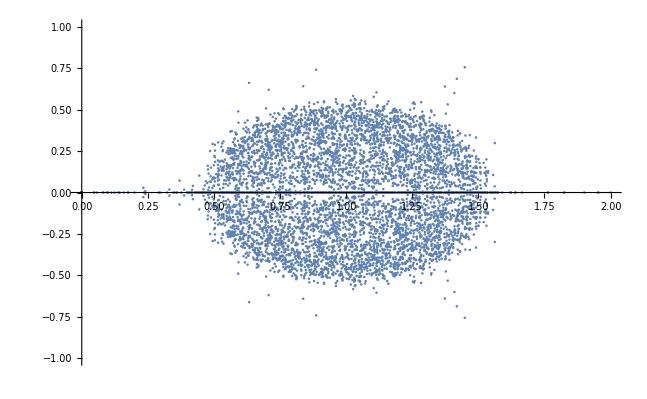

```mathematica
summaryEigenPlot = ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@Flatten@complexEigenSeries,PlotRange->{{0,2},{-1,1}}]
```

```mathematica
ruleSet[[489]]
```

{{1,2},{3,2}}→{{1,3},{3,2}}